# Tunning of NMR System

## Simulation on difference NMR setting and the method on Tunning

## *Need a phase shift

parameters are :
H = external field 
ω = NMR frequency 
L = level, somewhat equal to power 
t = pulse duration

2ndary parameters:
ω = γ H = Ω;
Ωμ = k L;

the Hamiltionian in the rotating frame is
HR = (Ω - ω) Iz + ωR Ix

```mathematica
γrad=267.5  (* Mrad/s/T *);
γ=42.577 ;(* MHz/T *)
```

```mathematica
(* the rotation axis is *)
RotAxis[Ω_,ω_,Ωμ_ ]:={Ωμ,0,Ω-ω}
```

```mathematica
(* Rotation operator *)
Ry[θ_]:={{Cos[θ],0,Sin[θ]},{0,1,0},{-Sin[θ],0,Cos[θ]}}
Rz[θ_]:={{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}
```

```mathematica
(* the locus that traced by the polarization vector *)
v[α_,θ_]:=Ry[θ].Rz[α].Ry[-θ].{0,0,1}//FullSimplify
v[α,θ]
```

{-(-1+Cos[α]) Cos[θ] Sin[θ],-Sin[α] Sin[θ],Cos[θ]^2+Cos[α] Sin[θ]^2}

```mathematica
(* Signal Amp *)
SigAmp[α_,θ_]:=√((v[α,θ][[1]])^2+ (v[α,θ][[2]])^2)
phase[α_,θ_]:=Arg[v[α,θ][[1]]+ⅈ v[α,θ][[2]]]
SigAmp[α,θ]//Simplify
phase[π/2,π/2]*180/π//N
```

√(((-1+Cos[α])^2 Cos[θ]^2+Sin[α]^2) Sin[θ]^2)

-90.

```mathematica
Plot[K,{α,0,360}] (* 1st pulse FID vs angle of rotation axis *)
```

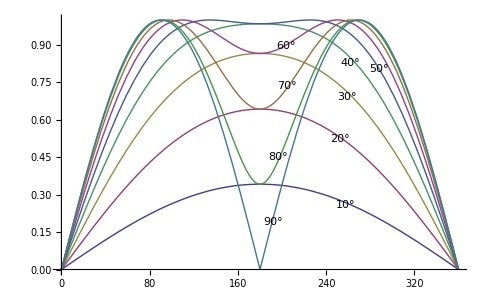

```mathematica
Manipulate[
Show[
Graphics3D[
{
Arrow[{{0,0,0},{0,0,1}}],
Arrow[{{0,0,0},{0,1,0}}],
Arrow[{{0,0,0},{1,0,0}}],
{Opacity[.3],Sphere[{0,0,0},1]},
{Green,Arrow[{{0,0,0},RotAxis[Ω,ω,Ωμ]}]},
{Blue,Arrow[{{0,0,0},v[t √((Ω-ω)^2+Ωμ^2),ArcTan[Ω-ω,Ωμ]]}]},
{Red,Arrow[{{0,0,0},{v[t √((Ω-ω)^2+Ωμ^2),ArcTan[Ω-ω,Ωμ]][[1]],v[t √((Ω-ω)^2+Ωμ^2),ArcTan[Ω-ω,Ωμ]][[2]],0}}]},
{Purple,Arrow[{{0,0,0},{0,0,v[t √((Ω-ω)^2+Ωμ^2),ArcTan[Ω-ω,Ωμ]][[3]]}}]}
},Boxed->False,ViewPoint->{1,1,1}],
ParametricPlot3D[{
v[a,ArcTan[Ω-ω,Ωμ]],
{v[a,ArcTan[Ω-ω,Ωμ]][[1]],v[a,ArcTan[Ω-ω,Ωμ]][[2]],0},
{Cos[a],Sin[a],0}}
,{a,0,2π}]
],{{Ω,1},0,1},{ω,0.1,1},{{Ωμ,0.5},0,1},{{t,1},0,10}]
```

## Filter

```mathematica
(* Low Pass Filter *)
Manipulate[Plot[1/(1+(ω/ω0)^2),{ω,0,10},PlotRange->{0,1}],{ω0,1,10}]
```

```mathematica
InverseFourierTransform[FourierTransform[Cos[Ω t0] Cos[ω t0+ϕ],t0,k] 1/(1+(k/ω0)^2),k,t]
InverseFourierTransform[FourierTransform[Cos[Ω t0] Sin[ω t0+ϕ],t0,k] 1/(1+(k/ω0)^2),k,t]
```

1/4 ⅇ^(-ⅈ ϕ) ω0^2 (((1+ⅇ^(2 ⅈ ϕ)) Cos[t (ω-Ω)])/(ω^2-2 ω Ω+Ω^2+ω0^2)+((1+ⅇ^(2 ⅈ ϕ)) Cos[t (ω+Ω)]+(2 ⅈ (-1+ⅇ^(2 ⅈ ϕ)) ((ω^2+Ω^2+ω0^2) Cos[t Ω] Sin[t ω]-2 ω Ω Cos[t ω] Sin[t Ω]))/(ω^2-2 ω Ω+Ω^2+ω0^2))/(ω^2+2 ω Ω+Ω^2+ω0^2))

1/4 ⅇ^(-ⅈ ϕ) ω0^2 (-(ⅈ (-1+ⅇ^(2 ⅈ ϕ)) Cos[t (ω-Ω)])/(ω^2-2 ω Ω+Ω^2+ω0^2)+(-ⅈ (-1+ⅇ^(2 ⅈ ϕ)) Cos[t (ω+Ω)]+(2 (1+ⅇ^(2 ⅈ ϕ)) ((ω^2+Ω^2+ω0^2) Cos[t Ω] Sin[t ω]-2 ω Ω Cos[t ω] Sin[t Ω]))/(ω^2-2 ω Ω+Ω^2+ω0^2))/(ω^2+2 ω Ω+Ω^2+ω0^2))

```mathematica
Manipulate[
Plot[{Cos[Ω t] Cos[ω t+ϕ],(g^2 ((ω^2+Ω^2+g^2) Cos[t ω+ϕ] Cos[t Ω]+2 ω Ω Sin[t ω+ϕ] Sin[t Ω]))/((ω^2-2 ω Ω+Ω^2+g^2) (ω^2+2 ω Ω+Ω^2+g^2))},{t,0,20},PlotRange->1],{{Ω,2},0,3},{ω,1,3},{g,0.1,3},{ϕ,0,π}](* g is the filiter frequency *)
```

```mathematica
(* for 2 freqeuncies signal *)
InverseFourierTransform[FourierTransform[Cos[Ω t0]( Cos[ω1 t0]+Cos[ω2 t0]),t0,k] 1/(1+(k/ω0)^2),k,t]
```

1/2 ω0^2 (Cos[t (Ω-ω1)]/(Ω^2+ω0^2-2 Ω ω1+ω1^2)+Cos[t (Ω+ω1)]/(Ω^2+ω0^2+2 Ω ω1+ω1^2)+Cos[t (Ω-ω2)]/(Ω^2+ω0^2-2 Ω ω2+ω2^2)+Cos[t (Ω+ω2)]/(Ω^2+ω0^2+2 Ω ω2+ω2^2))

```mathematica
1/2 ω0^2 (Cos[t (Ω-ω1)]/(Ω^2+ω0^2-2 Ω ω1+ω1^2)+Cos[t (Ω+ω1)]/(Ω^2+ω0^2+2 Ω ω1+ω1^2))
```

1/2 ω0^2 (Cos[t (Ω-ω1)]/(ω0^2+(Ω-ω1)^2)+Cos[t (Ω+ω1)]/(ω0^2+(Ω+ω1)^2))

```mathematica
(ω0^2 ((ω^2+Ω^2+ω0^2) Cos[t ω] Cos[t Ω]+2 ω Ω Sin[t ω] Sin[t Ω]))/((ω^2-2 ω Ω+Ω^2+ω0^2) (ω^2+2 ω Ω+Ω^2+ω0^2))/(1/2 ω0^2 (Cos[t (Ω-ω)]/(ω0^2+(Ω-ω)^2)+Cos[t (Ω+ω)]/(ω0^2+(Ω+ω)^2)))//Simplify
```

1

## Process of NMR raw signal

```mathematica
(* the simple sigle freqeuncy NMR raw signal is *)
S[t_,T2_,Ω_,ω_,Ωμ_,T_]:=SigAmp[T √((Ω-ω)^2+Ωμ^2),ArcTan[Ω-ω,Ωμ]]Exp[-t/T2]Cos[Ω t]
RefSin[ω_,t_]:=Sin[ω t]
RefCos[ω_,t_]:=Cos[ω t]
```

```mathematica
Manipulate[GraphicsGrid[{{
Show[Graphics3D[{
Arrow[{{0,0,0},{0,0,1}}],
Arrow[{{0,0,0},{0,1,0}}],
Arrow[{{0,0,0},{1,0,0}}],
{Opacity[.3],Sphere[{0,0,0},1]},
{Green,Arrow[{{0,0,0},RotAxis[Ω,ω,Ωμ]}]},
{Blue,Arrow[{{0,0,0},v[T √((Ω-ω)^2+Ωμ^2),ArcTan[Ω-ω,Ωμ]]}]},
{Red,Arrow[{{0,0,0},{v[T √((Ω-ω)^2+Ωμ^2),ArcTan[Ω-ω,Ωμ]][[1]],v[T √((Ω-ω)^2+Ωμ^2),ArcTan[Ω-ω,Ωμ]][[2]],0}}]},
{Purple,Arrow[{{0,0,0},{0,0,v[T √((Ω-ω)^2+Ωμ^2),ArcTan[Ω-ω,Ωμ]][[3]]}}]}
},Boxed->False,ViewPoint->{1,1,1},ImageSize->400,AspectRatio->1],
ParametricPlot3D[{
v[a,ArcTan[Ω-ω,Ωμ]],
{v[a,ArcTan[Ω-ω,Ωμ]][[1]],v[a,ArcTan[Ω-ω,Ωμ]][[2]],0},
{Cos[a],Sin[a],0}}
,{a,0,2π},PlotStyle->{Blue,Red,Black}]],
Plot[
{SigAmp[T √((Ω-ω)^2+Ωμ^2),ArcTan[Ω-ω,Ωμ]]Exp[-t/T2](ω0^2 ((ω^2+Ω^2+ω0^2) Cos[t Ω] Sin[t ω+phase[T √((Ω-ω)^2+Ωμ^2),ArcTan[Ω-ω,Ωμ]]]-2 ω Ω Cos[t ω+phase[T √((Ω-ω)^2+Ωμ^2),ArcTan[Ω-ω,Ωμ]]] Sin[t Ω]))/((ω^2-2 ω Ω+Ω^2+ω0^2) (ω^2+2 ω Ω+Ω^2+ω0^2)),
SigAmp[T √((Ω-ω)^2+Ωμ^2),ArcTan[Ω-ω,Ωμ]]Exp[-t/T2] (ω0^2 ((ω^2+Ω^2+ω0^2) Cos[t ω+phase[T √((Ω-ω)^2+Ωμ^2),ArcTan[Ω-ω,Ωμ]]] Cos[t Ω]+2 ω Ω Sin[t ω+phase[T √((Ω-ω)^2+Ωμ^2),ArcTan[Ω-ω,Ωμ]]] Sin[t Ω]))/((ω^2-2 ω Ω+Ω^2+ω0^2) (ω^2+2 ω Ω+Ω^2+ω0^2))
},{t,0,100},PlotRange->0.5,ImageSize->400,GridLines->Automatic]
}}],{{Ω,1},0,2},{{ω,0.8},0.1,2},{{Ωμ,0.5},0,1},{{T,3},0,10},{{T2,40},0.1,100},{{ω0,0.3},0.1,5}]
```

## Noise Generation

```mathematica
Random[Real,{-0.1,0.1}]
```

0.0452192

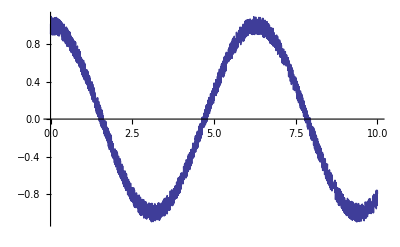

```mathematica
Plot[{Cos[ t]+Random[Real,1/10{-UnitStep[t],UnitStep[t]}]},{t,0,10}]
```

```mathematica
Noise[t_,noise_]:=Random[Real,noise{-UnitStep[t],UnitStep[t]}]
```

```mathematica
Manipulate[Plot[Mean[Table[Noise[t,0.1],{n,1,j,1}]],{t,0,10},PlotRange->0.1],{j,1,10}]
```

```mathematica
Nlist=Table[Noise[t,1],{t,0,10,0.01}];
```

0.0113939

0.58787

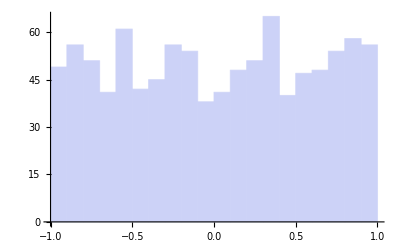

```mathematica
Mean[Nlist]
StandardDeviation[Nlist]
Histogram[Nlist,{0.1}]
```

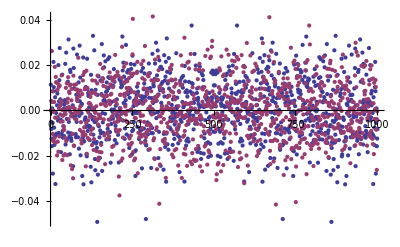

```mathematica
FTNlist=Fourier[Nlist,FourierParameters-> {-1,1}];
ListPlot[{Re[FTNlist],Im[FTNlist]}]
```

```mathematica
0.003/42.577
```

0.0000704606

## The "π" pulse or reversion of the pol vector

```mathematica
v[α,θ]
```

{-(-1+Cos[α]) Cos[θ] Sin[θ],-Sin[α] Sin[θ],Cos[θ]^2+Cos[α] Sin[θ]^2}

```mathematica
AA[n_,v_]:=√((v[[1]])^2+(v[[2]])^2)//Simplify
Rot[v_]:=Ry[θ].Rz[α].Ry[-θ].{0,0,v[[3]]}
```

```mathematica
(* initial pol vector *)
u[0]={0,0,1};
```

```mathematica
(* generate rotated vector and its AMp *)
Table[{u[n]=Rot[u[n-1]],AA[n-1,u[n-1]]},{n,1,5}];
```

```mathematica
(* List Out the rotated vector *)
Table[u[n],{n,0,5}]
```

{{0,0,1},{Cos[θ] Sin[θ]-Cos[α] Cos[θ] Sin[θ],-Sin[α] Sin[θ],Cos[θ]^2+Cos[α] Sin[θ]^2},{(Cos[θ] Sin[θ]-Cos[α] Cos[θ] Sin[θ]) (Cos[θ]^2+Cos[α] Sin[θ]^2),-Sin[α] Sin[θ] (Cos[θ]^2+Cos[α] Sin[θ]^2),(Cos[θ]^2+Cos[α] Sin[θ]^2)^2},{(Cos[θ] Sin[θ]-Cos[α] Cos[θ] Sin[θ]) (Cos[θ]^2+Cos[α] Sin[θ]^2)^2,-Sin[α] Sin[θ] (Cos[θ]^2+Cos[α] Sin[θ]^2)^2,(Cos[θ]^2+Cos[α] Sin[θ]^2)^3},{(Cos[θ] Sin[θ]-Cos[α] Cos[θ] Sin[θ]) (Cos[θ]^2+Cos[α] Sin[θ]^2)^3,-Sin[α] Sin[θ] (Cos[θ]^2+Cos[α] Sin[θ]^2)^3,(Cos[θ]^2+Cos[α] Sin[θ]^2)^4},{(Cos[θ] Sin[θ]-Cos[α] Cos[θ] Sin[θ]) (Cos[θ]^2+Cos[α] Sin[θ]^2)^4,-Sin[α] Sin[θ] (Cos[θ]^2+Cos[α] Sin[θ]^2)^4,(Cos[θ]^2+Cos[α] Sin[θ]^2)^5}}

```mathematica
Manipulate[
Show[
Graphics3D[
{
{Opacity[.3],Sphere[{0,0,0},1]},
{Green,Arrow[{{0,0,0},{Sin[θ],0,Cos[θ]}}]},
Arrow[{{0,0,0},{0,0,1}}],
Arrow[{{0,0,0},{0,1,0}}],
Arrow[{{0,0,0},{1,0,0}}],
{RGBColor[1,0,0],Arrow[{{0,0,0},{Cos[θ] Sin[θ]-Cos[α] Cos[θ] Sin[θ],-Sin[α] Sin[θ],0}}]},
{RGBColor[1,0,1],Arrow[{{0,0,0},{0,0,Cos[θ]^2+Cos[α] Sin[θ]^2}}]},
{RGBColor[0,0.5,1],Arrow[{{0,0,0},{(Cos[θ] Sin[θ]-Cos[α] Cos[θ] Sin[θ]) (Cos[θ]^2+Cos[α] Sin[θ]^2),-Sin[α] Sin[θ] (Cos[θ]^2+Cos[α] Sin[θ]^2),(Cos[θ]^2+Cos[α] Sin[θ]^2)^2}}]},
{RGBColor[1,0.5,0],Arrow[{{0,0,0},{(Cos[θ] Sin[θ]-Cos[α] Cos[θ] Sin[θ]) (Cos[θ]^2+Cos[α] Sin[θ]^2),-Sin[α] Sin[θ] (Cos[θ]^2+Cos[α] Sin[θ]^2),0}}]},
{RGBColor[0.7,0.1,0.7],Arrow[{{0,0,0},{0,0,(Cos[θ]^2+Cos[α] Sin[θ]^2)^2}}]},
{RGBColor[0,0,1],Arrow[{{0,0,0},{Cos[θ] Sin[θ]-Cos[α] Cos[θ] Sin[θ],-Sin[α] Sin[θ],Cos[θ]^2+Cos[α] Sin[θ]^2}}]}
},Boxed->False,ViewPoint->{1,1,0.6},AspectRatio->1],
ParametricPlot3D[{
{Cos[θ] Sin[θ]-Cos[a] Cos[θ] Sin[θ],-Sin[a] Sin[θ],Cos[θ]^2+Cos[a] Sin[θ]^2},
{Cos[θ] Sin[θ]-Cos[a] Cos[θ] Sin[θ],-Sin[a] Sin[θ],0},
{Cos[a],Sin[a],0},
{(Cos[θ] Sin[θ]-Cos[a] Cos[θ] Sin[θ]) (Cos[θ]^2+Cos[a] Sin[θ]^2),-Sin[a] Sin[θ] (Cos[θ]^2+Cos[a] Sin[θ]^2),0}}
,{a,0,2π},PlotStyle->{RGBColor[0,0,1],RGBColor[1,0,0],RGBColor[0,0,0],RGBColor[1,0.5,0]}]
],{α,0,2π},{{θ,π/3},0,π/2}]
```

```mathematica
(*List out the Amp *)
Simplify[Table[{n-1,AA[n-1,u[n-1]]},{n,1,5}],{Sin[θ]>0&& (Cos[θ]^2+Cos[α] Sin[θ]^2)>0}]
```

{{0,0},{1,√((-1+Cos[α])^2 Cos[θ]^2+Sin[α]^2) Sin[θ]},{2,√(4 Cos[θ]^2 Sin[α/2]^4+Sin[α]^2) Sin[θ] (Cos[θ]^2+Cos[α] Sin[θ]^2)},{3,√(4 Cos[θ]^2 Sin[α/2]^4+Sin[α]^2) Sin[θ] (Cos[θ]^2+Cos[α] Sin[θ]^2)^2},{4,√(4 Cos[θ]^2 Sin[α/2]^4+Sin[α]^2) Sin[θ] (Cos[θ]^2+Cos[α] Sin[θ]^2)^3}}

```mathematica
Manipulate[ListLogPlot[Table[(Cos[θ]^2+Cos[α] Sin[θ]^2)^n,{n,0,5}]
,Joined->True,PlotRange->{0,1},PlotMarkers-> {"×",Large}],{α,0.1, π},{{θ,1},0,π/2}]
```

```mathematica
Manipulate[Plot[{Abs[√((-1+Cos[α °])^2 Cos[θ °]^2+Sin[α °]^2) Sin[θ °]](* 2st pulse FID*),
Abs[√(4 Cos[θ °]^2 Sin[(α °)/2]^4+Sin[α °]^2) Sin[θ °] (Cos[θ °]^2+Cos[α °] Sin[θ °]^2)](* 2nd Pulse *)}
,{α,0,360},PlotRange->{0,1},GridLines->{{90,180,270},{0.5,1}}],{{θ,60,"angle of rotation axia"},0,90}]
```

```mathematica
(* Ratio of n-th and n+1-th pulse *)
Manipulate[Plot[Abs[Cos[θ °]^2+Cos[α °] Sin[θ °]^2],{α,0,360},PlotRange->{0,1},GridLines->{{90,180,270},{0.5,1}}],{{θ,60},0,90}]
```

```mathematica
Solve[ArcCos[-Cot[θ °]^2]/(2π-ArcCos[-Cot[θ °]^2])==0.41,θ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ→-63.2783},{θ→63.2783}}

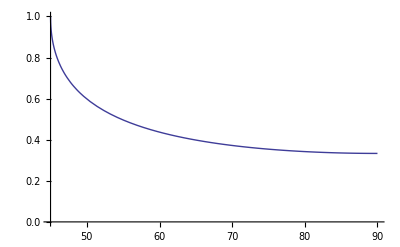

```mathematica
Plot[ArcCos[-Cot[θ °]^2]/(2π-ArcCos[-Cot[θ °]^2]),{θ,45,90},PlotRange->{{45,90},{0,1}},AxesOrigin->{45,0}]
```

## Signal of 2 freqeuncies

```mathematica
(* a simple picture is by 2 rotation axis *)
(* the polarization divide half on this *)
```

```mathematica
FourierTransform[Exp[-ⅈ ω t]Exp[(-Abs[t])/T],t,k]//FullSimplify
```

(√(2/π) T)/(1+T^2 (k-ω)^2)

```mathematica
Manipulate[
{Plot[(√(2/π) T)/(1+T^2 (k+ω1)^2)+(√(2/π) T)/(1+T^2 (k+ω1+a)^2),{k,-10,10},PlotRange->All,ImageSize->400],
Plot[{Re[Exp[ⅈ ω1 t]Exp[(-Abs[t])/T]+Exp[ⅈ (ω1+a) t]Exp[(-Abs[t])/T]],Im[Exp[ⅈ ω1 t]Exp[(-Abs[t])/T]+Exp[ⅈ (ω1+a) t]Exp[(-Abs[t])/T]]},{t,0,10},PlotRange->{-2,2},ImageSize->400]},{T,1,5},{ω1,-4,4},{a,-10,10}]
```

```mathematica
Manipulate[GraphicsGrid[{{
Show[Graphics3D[{
Arrow[{{0,0,0},{0,0,1}}],
Arrow[{{0,0,0},{0,1,0}}],
Arrow[{{0,0,0},{1,0,0}}],
{Opacity[.3],Sphere[{0,0,0},1]},
{Green,Arrow[{{0,0,0},RotAxis[Ω,ω1,Ωμ]}]},
{Blue,Arrow[{{0,0,0},v[T √((Ω-ω1)^2+Ωμ^2),ArcTan[Ω-ω1,Ωμ]]}]},
{Red,Arrow[{{0,0,0},{v[T √((Ω-ω1)^2+Ωμ^2),ArcTan[Ω-ω1,Ωμ]][[1]],v[T √((Ω-ω1)^2+Ωμ^2),ArcTan[Ω-ω1,Ωμ]][[2]],0}}]},
{Purple,Arrow[{{0,0,0},{0,0,v[T √((Ω-ω1)^2+Ωμ^2),ArcTan[Ω-ω1,Ωμ]][[3]]}}]},
{Green,Arrow[{{0,0,0},RotAxis[Ω,ω2,Ωμ]}]},
{Blue,Arrow[{{0,0,0},v[T √((Ω-ω2)^2+Ωμ^2),ArcTan[Ω-ω2,Ωμ]]}]},
{Red,Arrow[{{0,0,0},{v[T √((Ω-ω2)^2+Ωμ^2),ArcTan[Ω-ω2,Ωμ]][[1]],v[T √((Ω-ω2)^2+Ωμ^2),ArcTan[Ω-ω2,Ωμ]][[2]],0}}]},
{Purple,Arrow[{{0,0,0},{0,0,v[T √((Ω-ω2)^2+Ωμ^2),ArcTan[Ω-ω2,Ωμ]][[3]]}}]}
},Boxed->False,ViewPoint->{1,1,0.7},ImageSize->400,AspectRatio->1],
ParametricPlot3D[{
v[a,ArcTan[Ω-ω1,Ωμ]],
{v[a,ArcTan[Ω-ω1,Ωμ]][[1]],v[a,ArcTan[Ω-ω1,Ωμ]][[2]],0},
v[a,ArcTan[Ω-ω2,Ωμ]],
{v[a,ArcTan[Ω-ω2,Ωμ]][[1]],v[a,ArcTan[Ω-ω2,Ωμ]][[2]],0},
{Cos[a],Sin[a],0}}
,{a,0,2π},PlotStyle->{Blue,Red,Blue,Red,Black}]],
Plot[
{SigAmp[T √((Ω-ω1)^2+Ωμ^2),ArcTan[Ω-ω1,Ωμ]]Exp[-t/T2](ω0^2 ((ω1^2+Ω^2+ω0^2) Cos[t Ω] Sin[t ω1+phase[T √((Ω-ω1)^2+Ωμ^2),ArcTan[Ω-ω1,Ωμ]]]-2 ω1 Ω Cos[t ω1+phase[T √((Ω-ω1)^2+Ωμ^2),ArcTan[Ω-ω1,Ωμ]]] Sin[t Ω]))/((ω1^2-2 ω1 Ω+Ω^2+ω1^2) (ω1^2+2 ω1 Ω+Ω^2+ω0^2))+SigAmp[T √((Ω-ω2)^2+Ωμ^2),ArcTan[Ω-ω2,Ωμ]]Exp[-t/T2](ω0^2 ((ω2^2+Ω^2+ω0^2) Cos[t Ω] Sin[t ω2+phase[T √((Ω-ω2)^2+Ωμ^2),ArcTan[Ω-ω2,Ωμ]]]-2 ω2 Ω Cos[t ω2+phase[T √((Ω-ω2)^2+Ωμ^2),ArcTan[Ω-ω2,Ωμ]]] Sin[t Ω]))/((ω2^2-2 ω2 Ω+Ω^2+ω0^2) (ω2^2+2 ω2 Ω+Ω^2+ω0^2)),
SigAmp[T √((Ω-ω1)^2+Ωμ^2),ArcTan[Ω-ω1,Ωμ]]Exp[-t/T2] (ω0^2 ((ω1^2+Ω^2+ω0^2) Cos[t ω1+phase[T √((Ω-ω1)^2+Ωμ^2),ArcTan[Ω-ω1,Ωμ]]] Cos[t Ω]+2 ω1 Ω Sin[t ω1+phase[T √((Ω-ω1)^2+Ωμ^2),ArcTan[Ω-ω1,Ωμ]]] Sin[t Ω]))/((ω1^2-2 ω1 Ω+Ω^2+ω0^2) (ω1^2+2 ω1 Ω+Ω^2+ω0^2))+SigAmp[T √((Ω-ω2)^2+Ωμ^2),ArcTan[Ω-ω2,Ωμ]]Exp[-t/T2] (ω0^2 ((ω2^2+Ω^2+ω0^2) Cos[t ω2+phase[T √((Ω-ω2)^2+Ωμ^2),ArcTan[Ω-ω2,Ωμ]]] Cos[t Ω]+2 ω2 Ω Sin[t ω2+phase[T √((Ω-ω2)^2+Ωμ^2),ArcTan[Ω-ω2,Ωμ]]] Sin[t Ω]))/((ω2^2-2 ω2 Ω+Ω^2+ω0^2) (ω2^2+2 ω2 Ω+Ω^2+ω0^2))
},{t,0,100},PlotRange->0.5,ImageSize->400,GridLines->Automatic]
}}],{{Ω,1},0,2},{{ω1,0.8},0.1,2},{{ω2,1.2},0.1,2},{{Ωμ,0.5},0,1},{{T,3},0,10},{{T2,40},0.1,100},{{ω0,0.5},0.1,5}]
```